### Rule Graphs

```mathematica
getsubs[{n_, k_, r_}]:= MapThread[#1->#2&, {Reverse[Tuples[Range[0, k - 1], 1 + 2r]],IntegerDigits[n, k, k^(2r+1)]}]
```

```mathematica
subs = getsubs[l1[[bmi[[1]], 1]]];
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 0], 3, 1]
```

```mathematica
init = CenterArray[1, 50];
```

```mathematica
tab = NestList[nextrus, Partition[init, 3, 1],200];
```

```mathematica
Module[{},
subs = getsubs[];
]
```

```mathematica
With[{ws =KeyDrop[Counts[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]]], {({0, 0, 0}->{0, 0, 0})}]},  Graph[KeyValueMap[Style[#1, Thickness[.001#2^.5]]&, ws], VertexShapeFunction->(Inset[ArrayPlot[{#2}, ImageSize->30, ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]], #1]&), EdgeWeight->Values[ws], GraphLayout->"SpringElectricalEmbedding"]]
```

### Progressive fitness from random inits replacing vals

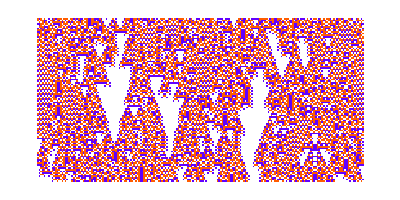
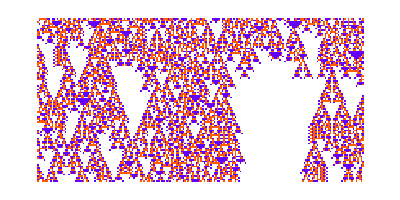
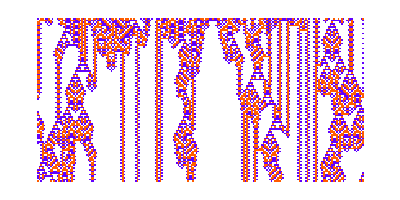
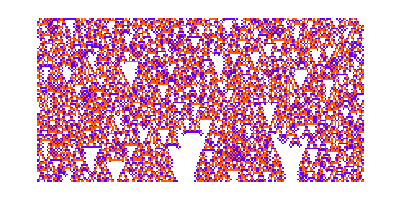
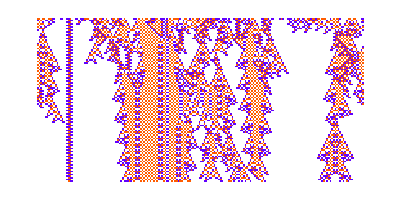
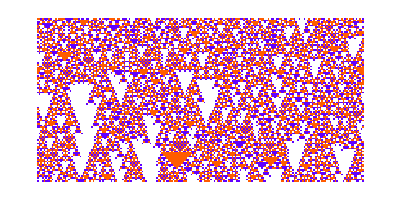
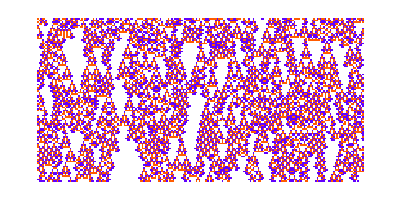
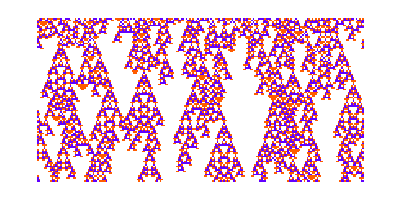
{-Graphics-162,-Graphics-97,-Graphics-72,-Graphics-67,-Graphics-59,-Graphics-59,-Graphics-54,-Graphics-53,-Graphics-50,-Graphics-45,-Graphics-42,-Graphics-40,-Graphics-39,-Graphics-38,-Graphics-37,-Graphics-35,-Graphics-31,-Graphics-30,-Graphics-28,-Graphics-27,-Graphics-27,-Graphics-26,-Graphics-26,-Graphics-24,-Graphics-24,-Graphics-24,-Graphics-23,-Graphics-23,-Graphics-23,-Graphics-22,-Graphics-22,-Graphics-22,-Graphics-21,-Graphics-21,-Graphics-21,-Graphics-19,-Graphics-19,-Graphics-19,-Graphics-18,-Graphics-18,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-17,-Graphics-16,-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-15,-Graphics-14,-Graphics-14,-Graphics-14,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-13,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-12,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-11,-Graphics-10,-Graphics-10,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-9,-Graphics-8,-Graphics-8,-Graphics-8,-Graphics-8,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-7,-Graphics-6,-Graphics-6,-Graphics-5,-Graphics-5,-Graphics-4}

```mathematica
KeyValueMap[Module[{ca = CellularAutomaton[{#1[[1]], 3, 1}, RandomInteger[2, 200], 100], lt},
lt =  {{"[◼]", "TestCALifeTime"}}[ca];Labeled[ArrayPlot[ca[[;;100]]], Text[#2]]]&,ReverseSort[RandomSample[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 100]]]
```

### Data compression

### Langton’s number

### Fractal dimension of lifelike patterns using image processing

```mathematica
img =-Graphics-;
```

```mathematica
getSeq[img_]:= Module[{},
bin=LocalAdaptiveBinarize[ImageAdjust[img,0.3],200,{0.9,0,0}];
seq=Reverse[Intersection@@Divisors/@ImageDimensions[img]]]
```

```mathematica
getSeq[img]
```

{10,5,2,1}

```mathematica
imgs=Image[BlockMap[Min,ImageData[bin],{#,#}],"Bit"]&/@seq
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
imgs=If[First@ImageDimensions[#]>sz,ImageResize[Image[#,Real],sz],(*downscale as grayscale*)ImageResize[#,sz,Resampling->"Nearest"]]&/@imgs(*upscale as bitmap*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
frm=Table[ImageCompose[ImageResize[img,252],{im,0.5}],{im,imgs}];
```

```mathematica
ListAnimate[frm]
```

```mathematica
aps = {-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50};
```

Null

```mathematica
Head[aps[[1, 1]]]
```

Graphics

```mathematica
img = Show[aps[[1, 1]], Frame->False]
```

-Graphics-

```mathematica
Table[ImageAdjust[img,i],{i, 0, 1,.1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[LocalAdaptiveBinarize[aps[[1, 1]],i,{0.9,0,0}], {i, 200, 400, 50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LocalAdaptiveBinarize[aps[[1, 1]],200,{0.9,0,0}]
```

-Graphics-

```mathematica
ImageDimensions[]
```

{41,177}

```mathematica
bin = ImageResize[LocalAdaptiveBinarize[img,200,{0.9,0,0}], {100, 500}]
```

-Graphics-

```mathematica
Divisors/@ImageDimensions[]
```

{{1,41},{1,3,59,177}}

```mathematica
seq=Reverse[Intersection@@Divisors/@ImageDimensions[]]
```

{100,50,25,20,10,5,4,2,1}

```mathematica
imgs=Image[BlockMap[Min,ImageData[],{#,#}],"Bit"]&/@seq
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sz = 300;
```

```mathematica
imgs=If[First@ImageDimensions[#]>sz,ImageResize[Image[#,Real],sz],(*downscale as grayscale*)ImageResize[#,sz,Resampling->"Nearest"]]&/@imgs(*upscale as bitmap*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{width,height}=ImageDimensions[]
```

{100,500}

```mathematica
result={width/#,Last@First@ImageLevels@Image[BlockMap[Min,ImageData[bin],{#,#}],"Bit"]}&/@seq
```

{{1,5},{2,20},{4,58},{5,84},{10,276},{20,912},{25,1386},{50,4706},{100,16904}}

```mathematica
ListLogLogPlot[result]
```

-Graphics-

#### Comparing with rule 30

```mathematica
S
```

```mathematica
i2 = ArrayPlot[CellularAutomaton[30,{{1}, 0}, {100, {-8, 8}}], ColorRules->Automatic]
```

-Graphics-

```mathematica
bin2 = ImageResize[LocalAdaptiveBinarize[i2,200,{0.9,0,0}], {100, 500}]
```

-Graphics-

```mathematica
seq=Reverse[Intersection@@Divisors/@ImageDimensions[]]
```

{100,50,25,20,10,5,4,2,1}

```mathematica
imgs=Image[BlockMap[Min,ImageData[i2],{#,#}],"Bit"]&/@seq
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
imgs=If[First@ImageDimensions[#]>sz,ImageResize[Image[#,Real],sz],(*downscale as grayscale*)ImageResize[#,sz,Resampling->"Nearest"]]&/@imgs(*upscale as bitmap*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
seq
```

{100,50,25,20,10,5,4,2,1}

```mathematica
Image[BlockMap[Min,ImageData[bin2],{1, 1}],"Bit"]
```

-Graphics-

```mathematica
result={width/#,Last@First@ImageLevels@Image[BlockMap[Min,ImageData[bin2],{#,#}],"Bit"]}&/@seq
```

{{1,5},{2,20},{4,79},{5,123},{10,470},{20,1524},{25,2181},{50,6569},{100,21525}}

```mathematica
ListLogLogPlot[result]
```

-Graphics-

```mathematica
ListPlot[result]
```

-Graphics-

```mathematica
Image[ArrayPlot[ConstantArray[1, {500, 200}], ColorRules->Automatic], "Bit"]
```

```mathematica
i3 = -Graphics-;
```

```mathematica
Image[ArrayPlot[ConstantArray[1, {500, 200}], ColorRules->Automatic], "Bit"]
```

```mathematica
seq=Reverse[Intersection@@Divisors/@ImageDimensions[i3]]
```

{3,1}

```mathematica
imgs=Image[BlockMap[Min,ImageData[i3],{#,#}],"Bit"]&/@seq
```

{-Graphics-,-Graphics-}

```mathematica
imgs=If[First@ImageDimensions[#]>sz,ImageResize[Image[#,Real],sz],(*downscale as grayscale*)ImageResize[#,sz,Resampling->"Nearest"]]&/@imgs(*upscale as bitmap*)
```

{-Graphics-,-Graphics-}

```mathematica
result={width/#,Last@First@ImageLevels@Image[BlockMap[Min,ImageData[bin2],{#,#}],"Bit"]}&/@seq
```

{{100/3,3375},{100,21525}}

```mathematica
ListLogLogPlot[result]
```

-Graphics-

### Attempt 2

```mathematica
evos = Module[
{goal=100,deep=5000,cut=200,ru,life,evo,res},
SeedRandom[23563];
res=ParallelTable[
evo=Nest[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],1,"Symmetric"->True],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal
]<=Abs[Last[#]-goal],{ru,life},#]
]&,{{0,5,1},0},deep];evo,200]
];
```

```mathematica
Iconize[evos]
```

```mathematica
Length@Select[evos,Last[#]==100&]
```

155

```mathematica
Options[ArrayHaussdorfDimension] = {"CoarseGrainingFunction"-> Max}
ArrayHaussdorfDimension[arr_]:=Module[{},
seq = Reverse[Intersection@@Divisors/@Dimensions[arr]];

]
```

```mathematica
Unitize[{0, 1, 2}]
```

{0,1,1}

```mathematica
ArrayPlot@RandomInteger[2, {200, 300}]
```

-Graphics-

```mathematica
ArrayPlot@*Unitize@RandomInteger[2, {200, 300}]
```

-Graphics-

```mathematica
Map[]
```

```mathematica
Dimensions@RandomInteger[2, {200, 300}]
```

{200,300}

```mathematica
Divisors/@
```

```mathematica
Intersection@@Divisors/@Dimensions[arr]
```

### Image Analysis

```mathematica
KeyValueMap[Module[{ca = CellularAutomaton[{#1[[1]], 3, 1}, RandomInteger[2, 200], 100], lt},
lt =  {{"[◼]", "TestCALifeTime"}}[ca];Labeled[ArrayPlot[ca[[;;100]]], Text[#2]]]&,ReverseSort[RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], # >100&], 3]]]
```

{-Graphics-541,-Graphics-441,-Graphics-361}

```mathematica
KeyValueMap[CellularAutomaton[{#1[[1]], 3, 1}, RandomInteger[2, 200], 100]&,RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], # >100&],1]]]
```

-Graphics-

```mathematica
KeyValueMap[ArrayPlot@CellularAutomaton[{#1[[1]], 3, 1}, RandomInteger[2, 200], 100]&,RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], # >100&],1]]
```

{-Graphics-}

```mathematica
Binarize/@
```

{-Graphics-}

```mathematica
MorphologicalGraph/@
```

{-Graphics-}

Random for comparison

```mathematica
MorphologicalGraph[ArrayPlot[RandomInteger[1, {100, 200}], ColorRules->Automatic]]
```

-Graphics-

```mathematica
SkeletonTransform/@
```

{-Graphics-}

```mathematica
SkeletonTransform[ArrayPlot[RandomInteger[1, {100, 200}], ColorRules->Automatic]]
```

-Graphics-

```mathematica
ImageHistogram/@
```

{-Graphics-}

```mathematica
Colorize@*MorphologicalComponents/@
```

{-Graphics-}

```mathematica
Colorize@*ClusteringComponents/@
```

{-Graphics-}

```mathematica
CrossingDetect[Rasterize[#]]&/@
```

{-Graphics-}

```mathematica
Manipulate[GeodesicDilation[-Graphics-, -Graphics-, n], {n, 0, 20, 1}]
```

### Attempt 3

```mathematica
seq = Reverse[Intersection@@Divisors/@Dimensions[arr]];
```

```mathematica
arr =RandomInteger[1, {100, 200}];
```

```mathematica
2^7
```

128

```mathematica
ArrayPlot[#, ColorRules->Automatic, Mesh->True]&/@(Function[divs, BlockMap[Boole[Max[#]>= 1]&, arr, UpTo[Ceiling[# / divs]]&/@ Dimensions[arr]]]/@  Table[2^n, {n, 8}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Min[{{1, 2}, {3, 4}}]
```

1

```mathematica
Dimensions[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / 2]]&/@ Dimensions[arr]]]
```

{50,100}

{50,100}

{50,100}

«1 more identical outputs»

{2,2,50,100}

```mathematica
ArrayPlot[ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / 2]]&/@ Dimensions[arr]]], Mesh->True]
```

-Graphics-

```mathematica
ArrayPlot[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / 2]]&/@ Dimensions[arr]], ColorRules->Automatic, Mesh->True]
```

-Graphics-

```mathematica
ArrayPlot[#, ColorRules->Automatic, Mesh->True]&/@(Function[divs, BlockMap[Boole[Max[#]>= 1]&, arr,Echo[ UpTo[Ceiling[# / divs]]&/@ Dimensions[arr]]]]/@  Table[2^n, {n, 8}])
```

{UpTo[50],UpTo[100]}

{UpTo[25],UpTo[50]}

{UpTo[13],UpTo[25]}

{UpTo[7],UpTo[13]}

{UpTo[4],UpTo[7]}

{UpTo[2],UpTo[4]}

{UpTo[1],UpTo[2]}

{UpTo[1],UpTo[1]}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / divs]]&/@ Dimensions[arr]]]]/@ Table[2^n, {n, 7}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ca = KeyValueMap[CellularAutomaton[{#1[[1]], 3, 1}, RandomInteger[2, 200], 100]&,RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], # >100&],1]][[1]];
```

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, ca, UpTo[Ceiling[# / divs]]&/@ Dimensions[ca]]]]/@ Table[2^n, {n, 9}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(Function[divs, Count[ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, ca, UpTo[Ceiling[# / divs]]&/@ Dimensions[ca]]], 0, {2}]]/@ Table[2^n, {n, 9}])
```

{0,0,0,1071,2620,4112,6828,10135,10135}

```mathematica
(Function[divs, Count[ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, ca, UpTo[Ceiling[# / divs]]&/@ Dimensions[ca]]], 0, {2}]]/@ Table[2^n, {n, 9}])
```

```mathematica
Show[Plot[2^x, {x, 0, 8}, PlotStyle->Red], ListPlot[], PlotRange->All]
```

-Graphics-

```mathematica
ListLogLogPlot[]
```

-Graphics-

```mathematica
Show[Plot[2^x, {x, 0, 8}, PlotStyle->Red], ListPlot[], PlotRange->All]
```

```mathematica
Show[Plot[3^x, {x, 0, 9}, PlotStyle->Red], ListPlot[], PlotRange->All]
```

-Graphics-

```mathematica
Show[Plot[x^4.4, {x, 0, 9}, PlotStyle->Red], ListPlot[], PlotRange->All]
```

-Graphics-

```mathematica
Count[{{0, 1}, {0,0}}, 0, {2}]
```

3

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / divs]]&/@ Dimensions[arr]]]]/@ Table[2^n, {n, 7}])
```

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / divs]]&/@ Dimensions[arr]]]]/@ Table[2^n, {n, 7}])
```

```mathematica
RepeatedTiming[out  = (Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / divs]]&/@ Dimensions[arr]]]]/@ Table[2^n, {n, 7}]);]
```

{0.0625337,Null}

```mathematica
Options[ArrayHaussdorfDimension] = {"CoarseGrainingFunction"-> (Max[#]>= 1&), "ScalingExponent"->2}
ArrayHaussdorfDimension[arr_, n_:1]:=Module[{},
FoldWhileList[
Module[{res = BlockMap[OptionValue["CoarseGrainingFunction"], arr, UpTo[Round[# / OptionValue["ScalingExponent"]]]&/@ Dimensions[arr]]},
{Count[Flatten[res], True] / Length[res]

]
```

{CoarseGrainingFunction→Max,Null}

```mathematica
BlockMap[f, {{0,1, 0}, {1, 0, 1}}, {UpTo[2], UpTo[2]}]
```

{{f[{{0,1},{1,0}}],f[{{0},{1}}]}}

```mathematica
BlockMap[]
```

```mathematica
BlockMap[Total, RandomInteger[1, {100, 200}], {}]
```

```mathematica
ArrayPlot[RandomInteger[1, {100, 200}], ColorRules->Automatic]
```

-Graphics-

### Attempt 4

```mathematica
Table[ArrayPlot[CellularAutomaton[i, {{1}, 0},100]], {i, 30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[CellularAutomaton[i, {{1}, 0},127]], {i, {18}}]
```

{-Graphics-}

```mathematica
nest = CellularAutomaton[18, {{1}, 0},127];
```

```mathematica
arr =RandomInteger[1, {100, 200}];
```

```mathematica
(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, arr, UpTo[Ceiling[# / divs]]&/@ Dimensions[arr]]]]/@ Table[2^n, {n, 7}])
```

```mathematica
ca = KeyValueMap[CellularAutomaton[{#1[[1]], 3, 1}, RandomInteger[2, 200], 100]&,RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], # >100&],1]][[1]];
```

```mathematica
(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, ca, UpTo[Ceiling[# / divs]]&/@ Dimensions[ca]]]]/@ Table[2^n, {n, 9}])
```

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, nest, UpTo[Ceiling[# / divs]]&/@ Dimensions[nest]]]]/@ Table[2^n, {n,1, 9}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, nest, UpTo[Ceiling[# / divs]]&/@ Dimensions[nest]]]]/@ Table[2^n, {n,1, 9}]), ScalingFunctions->"Log"]
```

-Graphics-

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, ca, UpTo[Ceiling[# / divs]]&/@ Dimensions[ca]]]]/@ Table[2^n, {n,1, 9}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, nest, UpTo[Ceiling[# / divs]]&/@ Dimensions[nest]]]]/@ Table[2^n, {n,1, 9}]), ScalingFunctions->"Log"]
```

-Graphics-

```mathematica
evos[[All, 1]]
```

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ evos[[;;10, 1]])
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ evos[[;;1, 1]])
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[#, Mesh->True, MeshStyle->Opacity[.1]]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ evos[[;;1, 1]])
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

WIth Mesh

```mathematica
MapThread[ArrayPlot[#1,Mesh->#2, MeshStyle->Opacity[Length[#2[[1]]]^-.6]]&, {(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&@ (CellularAutomaton[#, {{1}, 0}, 105]&@ evos[[1, 1]]), Function[divs, Append[Table[i, {i, 0, # - 2,Ceiling[# / divs]}], #]&/@ Dimensions[CellularAutomaton[evos[[1, 1]], {{1}, 0}, 105]]]/@Table[2^n, {n,2, 7}]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Function[divs, Ceiling[# / divs]&/@ Dimensions[CellularAutomaton[evos[[1, 1]], {{1}, 0}, 200]]]/@Table[2^n, {n,2, 7}]]
```

-Graphics-

```mathematica
ListLinePlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ Select[evos, #[[2]] == 100&][[All, 1]]), PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ Select[evos, #[[2]] == 100&][[All, 1]]), PlotRange->All]
```

```mathematica
ListLinePlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ Select[evos, #[[2]] == 100&][[All, 1]]), PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics-

### Graphs of k = 5 symmetric from seed

```mathematica
MorphologicalGraph/@(ArrayPlot[CellularAutomaton[#, {{1}, 0}, 105]]&/@ evos[[;;10, 1]])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SkeletonTransform/@(ArrayPlot[CellularAutomaton[#, {{1}, 0}, 105]]&/@ evos[[;;10, 1]])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[evos, #[[2]] == 100&][[All, 1]] // Length
```

155

```mathematica
SeedRandom[333222];ParallelMap[ColorNegate[SkeletonTransform[ArrayPlot[CellularAutomaton[#, {{1}, 0}, 105]]]]&, Select[evos, #[[2]] == 100&][[All, 1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Blend[]
```

-Graphics-

```mathematica
Blend[RandomSample[, 10]]
```

-Graphics-